# XPS Data Processing

## 2021-03-15

Rule number 1: Press ctrl-s obsessively. I had a beautifully worded introduction here that I lost because Mathematica crashed. I’ll try to recreate it, but this is just a tribute.

This file represents the start of a paradigm shift in how I approach my scientific data processing. I’ll be the first to admit that I go through this process too often. I think that my data processing code isn’t well organized and is difficult to understand, so I’ll commit a full half day to changing it, only to find that it’s pretty much the same thing as what I had before and in another 2 months I’ll want to go through the same process again. This time will be different. Why? In part because of this file. This is a Mathematica Notebook but I’m treating it more like a notebook in the traditional “lab notebook” sense. Text that I write here will remain after it is written. Cells will be edited only if they result in insignificant errors. If it’s a learning opportunity, I’ll leave the error in there and write about why it occurred and how I think I’ll fix it.

As I reach usable code, the code will be transferred to a separate script or package file that I will use version control on. This way, I can always be sure to be able to analyze the data in exactly the same way that I did initially, even if I change the code later to improve it in some way, or change the way that the data is recorded, or something.

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"2021-03-15","data"}]]
FileNames[]
```

C:\Users\kahrendsen2\Box Sync\Gay Group\Project - Rb Spin Filter\karl\DataRuns\2021-03-15\data

{Au120sAged.xls,Au240s.xls,Au60s.xls,AuPreVacuum.xls,C0s.xls,C240s.xls,C60s.xls,formvar60s.xls}

```mathematica
Import["Au120sAged.xls"]
```

{{{,,,,,,,Acquisition Parameters :,,,,,Experiment Descriptions :},{,,,,,,,,,,,,  },{,,,,,,,Parameter, ,,,,Experiment\X-Ray011 400um - FG  ON\Au 120 s Aged},{,,,,,,,Total acquisition time,27.8 secs,,,,},{,,,,,,,Number of Scans,5.,,,,},{,,,,,,,Source Gun Type,Al K Alpha,,,,},115,{81.58,,38023.8,,,,,,,,,,},{81.48,,36713.7,,,,,,,,,,},{81.38,,35788.3,,,,,,,,,,},{81.28,,36207.3,,,,,,,,,,},{81.18,,35045.7,,,,,,,,,,},{81.08,,34982.5,,,,,,,,,,}},7,{{}}}
 |  |  |  |

```mathematica
im=%
```

{{{,,,,,,,Acquisition Parameters :,,,,,Experiment Descriptions :},{,,,,,,,,,,,,  },{,,,,,,,Parameter, ,,,,Experiment\X-Ray011 400um - FG  ON\Au 120 s Aged},{,,,,,,,Total acquisition time,27.8 secs,,,,},{,,,,,,,Number of Scans,5.,,,,},{,,,,,,,Source Gun Type,Al K Alpha,,,,},115,{81.58,,38023.8,,,,,,,,,,},{81.48,,36713.7,,,,,,,,,,},{81.38,,35788.3,,,,,,,,,,},{81.28,,36207.3,,,,,,,,,,},{81.18,,35045.7,,,,,,,,,,},{81.08,,34982.5,,,,,,,,,,}},7,{{}}}
 |  |  |  |

```mathematica
(* Just import the sheet names? *)
fn="Au120sAged.xls"
sn=Import[fn,"Sheets"](* sn = Sheet Names *)
```

Au120sAged.xls

{Au4f Scan,Na1s Scan,O1s Scan,N1s Scan,C1s Scan,S2p Scan,Peak Table,Titles,Sheet1}

```mathematica
(* Just import the gold data based on the sheet name *)
Import[fn,{sn[[1]]}]
```

Import::noelem: The Import element "Au4f Scan" is not present when importing as XLS.

$Failed

```mathematica
(* I think I have to specify that I want to import the "Data" element first.*)
ri=Import[fn,{"Data",sn[[1]]}](* ri = (R)aw (I)mport *)
```

{{,,,,,,,Acquisition Parameters :,,,,,Experiment Descriptions :},{,,,,,,,,,,,,  },{,,,,,,,Parameter, ,,,,Experiment\X-Ray011 400um - FG  ON\Au 120 s Aged},{,,,,,,,Total acquisition time,27.8 secs,,,,},{,,,,,,,Number of Scans,5.,,,,},{,,,,,,,Source Gun Type,Al K Alpha,,,,},{Axis,Energy,Elements=,111.,,,,Spot Size,400 µm,,,,},{,,,,,,,Lens Mode,Standard,,,,},{C:\Users\expert\Desktop\User data 2021\Ahrendsen\cysteineMultipleExposures\Experiment\X-Ray011 400um - FG  ON\Au 120 s Aged\Au4f Scan.VGD,,,,,,,Analyser Mode,CAE : Pass Energy 50.0 eV,,,,},{,,,,,,,Energy Step Size,0.100 eV,,,,},{,,,,,,,Number of Energy Steps,111.,,,,},{,,,,,,,,,,,,},{,,,,,,,,,,,,},{,,,,,,,,,,,,},{Binding Energy (E),,,,,,,,,,,,},{eV,,Counts / s,,,,,,,,,,},{92.08,,102001.,,,,,,,,,,},{91.98,,102787.,,,,,,,,,,},{91.88,,102706.,,,,,,,,,,},{91.78,,103571.,,,,,,,,,,},{91.68,,105603.,,,,,,,,,,},{91.58,,106420.,,,,,,,,,,},{91.48,,107323.,,,,,,,,,,},{91.38,,110144.,,,,,,,,,,},{91.28,,109995.,,,,,,,,,,},{91.18,,111388.,,,,,,,,,,},{91.08,,113061.,,,,,,,,,,},{90.98,,113587.,,,,,,,,,,},{90.88,,114653.,,,,,,,,,,},{90.78,,116765.,,,,,,,,,,},{90.68,,115620.,,,,,,,,,,},{90.58,,116516.,,,,,,,,,,},{90.48,,119144.,,,,,,,,,,},{90.38,,118177.,,,,,,,,,,},{90.28,,120997.,,,,,,,,,,},{90.18,,122364.,,,,,,,,,,},{90.08,,125047.,,,,,,,,,,},{89.98,,126648.,,,,,,,,,,},{89.88,,129543.,,,,,,,,,,},{89.78,,134421.,,,,,,,,,,},{89.68,,141073.,,,,,,,,,,},{89.58,,148304.,,,,,,,,,,},{89.48,,155469.,,,,,,,,,,},{89.38,,166625.,,,,,,,,,,},{89.28,,184097.,,,,,,,,,,},{89.18,,205058.,,,,,,,,,,},{89.08,,234200.,,,,,,,,,,},{88.98,,280305.,,,,,,,,,,},{88.88,,342659.,,,,,,,,,,},{88.78,,433886.,,,,,,,,,,},{88.68,,557714.,,,,,,,,,,},{88.58,,697253.,,,,,,,,,,},{88.48,,833614.,,,,,,,,,,},{88.38,,931991.,,,,,,,,,,},{88.28,,961807.,,,,,,,,,,},{88.18,,903461.,,,,,,,,,,},{88.08,,796545.,,,,,,,,,,},{87.98,,663466.,,,,,,,,,,},{87.88,,530422.,,,,,,,,,,},{87.78,,420126.,,,,,,,,,,},{87.68,,336652.,,,,,,,,,,},{87.58,,274450.,,,,,,,,,,},{87.48,,230752.,,,,,,,,,,},{87.38,,200114.,,,,,,,,,,},{87.28,,176921.,,,,,,,,,,},{87.18,,161632.,,,,,,,,,,},{87.08,,151710.,,,,,,,,,,},{86.98,,141304.,,,,,,,,,,},{86.88,,134624.,,,,,,,,,,},{86.78,,129504.,,,,,,,,,,},{86.68,,126554.,,,,,,,,,,},{86.58,,124120.,,,,,,,,,,},{86.48,,122757.,,,,,,,,,,},{86.38,,122265.,,,,,,,,,,},{86.28,,122515.,,,,,,,,,,},{86.18,,125830.,,,,,,,,,,},{86.08,,128428.,,,,,,,,,,},{85.98,,133565.,,,,,,,,,,},{85.88,,142514.,,,,,,,,,,},{85.78,,152419.,,,,,,,,,,},{85.68,,166809.,,,,,,,,,,},{85.58,,185325.,,,,,,,,,,},{85.48,,212983.,,,,,,,,,,},{85.38,,254355.,,,,,,,,,,},{85.28,,314535.,,,,,,,,,,},{85.18,,405304.,,,,,,,,,,},{85.08,,532803.,,,,,,,,,,},{84.98,,701837.,,,,,,,,,,},{84.88,,890647.,,,,,,,,,,},{84.78,,1.06778×10^6,,,,,,,,,,},{84.68,,1.17693×10^6,,,,,,,,,,},{84.58,,1.19081×10^6,,,,,,,,,,},{84.48,,1.09476×10^6,,,,,,,,,,},{84.38,,933288.,,,,,,,,,,},{84.28,,748131.,,,,,,,,,,},{84.18,,575196.,,,,,,,,,,},{84.08,,436345.,,,,,,,,,,},{83.98,,332706.,,,,,,,,,,},{83.88,,257199.,,,,,,,,,,},{83.78,,202166.,,,,,,,,,,},{83.68,,163311.,,,,,,,,,,},{83.58,,136534.,,,,,,,,,,},{83.48,,117028.,,,,,,,,,,},{83.38,,101366.,,,,,,,,,,},{83.28,,91101.7,,,,,,,,,,},{83.18,,82084.1,,,,,,,,,,},{83.08,,74431.6,,,,,,,,,,},{82.98,,68843.7,,,,,,,,,,},{82.88,,64255.3,,,,,,,,,,},{82.78,,59661.3,,,,,,,,,,},{82.68,,55553.1,,,,,,,,,,},{82.58,,53703.5,,,,,,,,,,},{82.48,,50690.5,,,,,,,,,,},{82.38,,48178.4,,,,,,,,,,},{82.28,,45588.,,,,,,,,,,},{82.18,,44513.2,,,,,,,,,,},{82.08,,43182.3,,,,,,,,,,},{81.98,,41664.6,,,,,,,,,,},{81.88,,40197.8,,,,,,,,,,},{81.78,,39698.7,,,,,,,,,,},{81.68,,38713.1,,,,,,,,,,},{81.58,,38023.8,,,,,,,,,,},{81.48,,36713.7,,,,,,,,,,},{81.38,,35788.3,,,,,,,,,,},{81.28,,36207.3,,,,,,,,,,},{81.18,,35045.7,,,,,,,,,,},{81.08,,34982.5,,,,,,,,,,}}

```mathematica
(* Playing around a bit here to find where the actual data starts and *)
jd =ri[[17;;]] (* jd = (J)ust (D)ata *)
(* Picking out just the columsn with numbers that we want *)
op=jd[[All,{1,3}]] (* op= (O)rdered (P)airs, these are the things that can be directly plotted. Kinda want to have a better name for these *)
```

{{92.08,,102001.,,,,,,,,,,},{91.98,,102787.,,,,,,,,,,},{91.88,,102706.,,,,,,,,,,},{91.78,,103571.,,,,,,,,,,},{91.68,,105603.,,,,,,,,,,},{91.58,,106420.,,,,,,,,,,},{91.48,,107323.,,,,,,,,,,},{91.38,,110144.,,,,,,,,,,},{91.28,,109995.,,,,,,,,,,},{91.18,,111388.,,,,,,,,,,},{91.08,,113061.,,,,,,,,,,},{90.98,,113587.,,,,,,,,,,},{90.88,,114653.,,,,,,,,,,},{90.78,,116765.,,,,,,,,,,},{90.68,,115620.,,,,,,,,,,},{90.58,,116516.,,,,,,,,,,},{90.48,,119144.,,,,,,,,,,},{90.38,,118177.,,,,,,,,,,},{90.28,,120997.,,,,,,,,,,},{90.18,,122364.,,,,,,,,,,},{90.08,,125047.,,,,,,,,,,},{89.98,,126648.,,,,,,,,,,},{89.88,,129543.,,,,,,,,,,},{89.78,,134421.,,,,,,,,,,},{89.68,,141073.,,,,,,,,,,},{89.58,,148304.,,,,,,,,,,},{89.48,,155469.,,,,,,,,,,},{89.38,,166625.,,,,,,,,,,},{89.28,,184097.,,,,,,,,,,},{89.18,,205058.,,,,,,,,,,},{89.08,,234200.,,,,,,,,,,},{88.98,,280305.,,,,,,,,,,},{88.88,,342659.,,,,,,,,,,},{88.78,,433886.,,,,,,,,,,},{88.68,,557714.,,,,,,,,,,},{88.58,,697253.,,,,,,,,,,},{88.48,,833614.,,,,,,,,,,},{88.38,,931991.,,,,,,,,,,},{88.28,,961807.,,,,,,,,,,},{88.18,,903461.,,,,,,,,,,},{88.08,,796545.,,,,,,,,,,},{87.98,,663466.,,,,,,,,,,},{87.88,,530422.,,,,,,,,,,},{87.78,,420126.,,,,,,,,,,},{87.68,,336652.,,,,,,,,,,},{87.58,,274450.,,,,,,,,,,},{87.48,,230752.,,,,,,,,,,},{87.38,,200114.,,,,,,,,,,},{87.28,,176921.,,,,,,,,,,},{87.18,,161632.,,,,,,,,,,},{87.08,,151710.,,,,,,,,,,},{86.98,,141304.,,,,,,,,,,},{86.88,,134624.,,,,,,,,,,},{86.78,,129504.,,,,,,,,,,},{86.68,,126554.,,,,,,,,,,},{86.58,,124120.,,,,,,,,,,},{86.48,,122757.,,,,,,,,,,},{86.38,,122265.,,,,,,,,,,},{86.28,,122515.,,,,,,,,,,},{86.18,,125830.,,,,,,,,,,},{86.08,,128428.,,,,,,,,,,},{85.98,,133565.,,,,,,,,,,},{85.88,,142514.,,,,,,,,,,},{85.78,,152419.,,,,,,,,,,},{85.68,,166809.,,,,,,,,,,},{85.58,,185325.,,,,,,,,,,},{85.48,,212983.,,,,,,,,,,},{85.38,,254355.,,,,,,,,,,},{85.28,,314535.,,,,,,,,,,},{85.18,,405304.,,,,,,,,,,},{85.08,,532803.,,,,,,,,,,},{84.98,,701837.,,,,,,,,,,},{84.88,,890647.,,,,,,,,,,},{84.78,,1.06778×10^6,,,,,,,,,,},{84.68,,1.17693×10^6,,,,,,,,,,},{84.58,,1.19081×10^6,,,,,,,,,,},{84.48,,1.09476×10^6,,,,,,,,,,},{84.38,,933288.,,,,,,,,,,},{84.28,,748131.,,,,,,,,,,},{84.18,,575196.,,,,,,,,,,},{84.08,,436345.,,,,,,,,,,},{83.98,,332706.,,,,,,,,,,},{83.88,,257199.,,,,,,,,,,},{83.78,,202166.,,,,,,,,,,},{83.68,,163311.,,,,,,,,,,},{83.58,,136534.,,,,,,,,,,},{83.48,,117028.,,,,,,,,,,},{83.38,,101366.,,,,,,,,,,},{83.28,,91101.7,,,,,,,,,,},{83.18,,82084.1,,,,,,,,,,},{83.08,,74431.6,,,,,,,,,,},{82.98,,68843.7,,,,,,,,,,},{82.88,,64255.3,,,,,,,,,,},{82.78,,59661.3,,,,,,,,,,},{82.68,,55553.1,,,,,,,,,,},{82.58,,53703.5,,,,,,,,,,},{82.48,,50690.5,,,,,,,,,,},{82.38,,48178.4,,,,,,,,,,},{82.28,,45588.,,,,,,,,,,},{82.18,,44513.2,,,,,,,,,,},{82.08,,43182.3,,,,,,,,,,},{81.98,,41664.6,,,,,,,,,,},{81.88,,40197.8,,,,,,,,,,},{81.78,,39698.7,,,,,,,,,,},{81.68,,38713.1,,,,,,,,,,},{81.58,,38023.8,,,,,,,,,,},{81.48,,36713.7,,,,,,,,,,},{81.38,,35788.3,,,,,,,,,,},{81.28,,36207.3,,,,,,,,,,},{81.18,,35045.7,,,,,,,,,,},{81.08,,34982.5,,,,,,,,,,}}

{{92.08,102001.},{91.98,102787.},{91.88,102706.},{91.78,103571.},{91.68,105603.},{91.58,106420.},{91.48,107323.},{91.38,110144.},{91.28,109995.},{91.18,111388.},{91.08,113061.},{90.98,113587.},{90.88,114653.},{90.78,116765.},{90.68,115620.},{90.58,116516.},{90.48,119144.},{90.38,118177.},{90.28,120997.},{90.18,122364.},{90.08,125047.},{89.98,126648.},{89.88,129543.},{89.78,134421.},{89.68,141073.},{89.58,148304.},{89.48,155469.},{89.38,166625.},{89.28,184097.},{89.18,205058.},{89.08,234200.},{88.98,280305.},{88.88,342659.},{88.78,433886.},{88.68,557714.},{88.58,697253.},{88.48,833614.},{88.38,931991.},{88.28,961807.},{88.18,903461.},{88.08,796545.},{87.98,663466.},{87.88,530422.},{87.78,420126.},{87.68,336652.},{87.58,274450.},{87.48,230752.},{87.38,200114.},{87.28,176921.},{87.18,161632.},{87.08,151710.},{86.98,141304.},{86.88,134624.},{86.78,129504.},{86.68,126554.},{86.58,124120.},{86.48,122757.},{86.38,122265.},{86.28,122515.},{86.18,125830.},{86.08,128428.},{85.98,133565.},{85.88,142514.},{85.78,152419.},{85.68,166809.},{85.58,185325.},{85.48,212983.},{85.38,254355.},{85.28,314535.},{85.18,405304.},{85.08,532803.},{84.98,701837.},{84.88,890647.},{84.78,1.06778×10^6},{84.68,1.17693×10^6},{84.58,1.19081×10^6},{84.48,1.09476×10^6},{84.38,933288.},{84.28,748131.},{84.18,575196.},{84.08,436345.},{83.98,332706.},{83.88,257199.},{83.78,202166.},{83.68,163311.},{83.58,136534.},{83.48,117028.},{83.38,101366.},{83.28,91101.7},{83.18,82084.1},{83.08,74431.6},{82.98,68843.7},{82.88,64255.3},{82.78,59661.3},{82.68,55553.1},{82.58,53703.5},{82.48,50690.5},{82.38,48178.4},{82.28,45588.},{82.18,44513.2},{82.08,43182.3},{81.98,41664.6},{81.88,40197.8},{81.78,39698.7},{81.68,38713.1},{81.58,38023.8},{81.48,36713.7},{81.38,35788.3},{81.28,36207.3},{81.18,35045.7},{81.08,34982.5}}

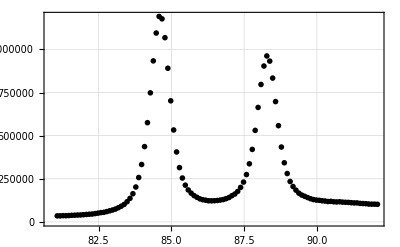

```mathematica
ListPlot[{op}]
```

Okay! I think we’ve mostly got something usable here. I’m going to go back and copy the necessary lines to put this all in one cell.

```mathematica
fn="Au120sAged.xls";
sn="S2p Scan";
(* Need to specify that we want the "Data" from the excel sheet, rather than the sheetnames or some other metadata.*)
ri=Import[fn,{"Data",sn}];(* ri = (R)aw (I)mport *)
jd =ri[[17;;]];(* jd = (J)ust (D)ata *)
op=jd[[All,{1,3}]] (* op= (O)rdered (P)airs *)
```

{{174.08,122278.},{173.98,122186.},{173.88,122847.},{173.78,122325.},{173.68,122412.},{173.58,122798.},{173.48,122224.},{173.38,122861.},{173.28,121563.},{173.18,122441.},{173.08,122640.},{172.98,122510.},{172.88,122285.},{172.78,122721.},{172.68,122755.},{172.58,122200.},{172.48,122493.},{172.38,122111.},{172.28,122442.},{172.18,122621.},{172.08,123259.},{171.98,122911.},{171.88,123442.},{171.78,123248.},{171.68,122282.},{171.58,123003.},{171.48,123562.},{171.38,123899.},{171.28,122731.},{171.18,123321.},{171.08,124171.},{170.98,123339.},{170.88,123960.},{170.78,124561.},{170.68,124959.},{170.58,124721.},{170.48,125449.},{170.38,125131.},{170.28,125520.},{170.18,125900.},{170.08,126255.},{169.98,126020.},{169.88,126033.},{169.78,126338.},{169.68,126183.},{169.58,127161.},{169.48,127213.},{169.38,127700.},{169.28,127833.},{169.18,127762.},{169.08,127615.},{168.98,127984.},{168.88,127770.},{168.78,127750.},{168.68,127608.},{168.58,127320.},{168.48,126763.},{168.38,127192.},{168.28,126528.},{168.18,125922.},{168.08,125983.},{167.98,125587.},{167.88,124856.},{167.78,124797.},{167.68,125358.},{167.58,124856.},{167.48,125480.},{167.38,125442.},{167.28,124414.},{167.18,124423.},{167.08,124047.},{166.98,124227.},{166.88,124025.},{166.78,124461.},{166.68,123813.},{166.58,124822.},{166.48,124216.},{166.38,124935.},{166.28,124792.},{166.18,124313.},{166.08,124465.},{165.98,124234.},{165.88,124092.},{165.78,124117.},{165.68,124295.},{165.58,124742.},{165.48,123843.},{165.38,123954.},{165.28,124656.},{165.18,124044.},{165.08,124472.},{164.98,124915.},{164.88,124883.},{164.78,124326.},{164.68,124429.},{164.58,124636.},{164.48,124689.},{164.38,125144.},{164.28,125791.},{164.18,124970.},{164.08,125372.},{163.98,125558.},{163.88,125444.},{163.78,126504.},{163.68,125412.},{163.58,125466.},{163.48,125403.},{163.38,125599.},{163.28,125719.},{163.18,126180.},{163.08,126367.},{162.98,126025.},{162.88,125861.},{162.78,125955.},{162.68,126510.},{162.58,125437.},{162.48,126680.},{162.38,126246.},{162.28,126235.},{162.18,126375.},{162.08,126340.},{161.98,126201.},{161.88,126259.},{161.78,126138.},{161.68,126299.},{161.58,126311.},{161.48,125971.},{161.38,126293.},{161.28,125793.},{161.18,125430.},{161.08,125328.},{160.98,125149.},{160.88,125382.},{160.78,125397.},{160.68,125267.},{160.58,125544.},{160.48,124845.},{160.38,125601.},{160.28,125907.},{160.18,126220.},{160.08,125580.}}

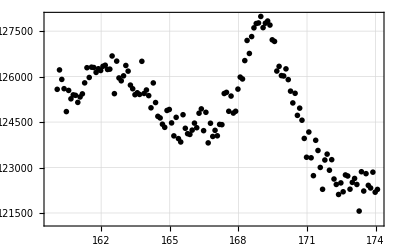

```mathematica
ListPlot[{op}]
```

Binding energy plots are typically plotted with BE increasing to the LEFT rather than the right, there should be an option in ListPlot to flip this.

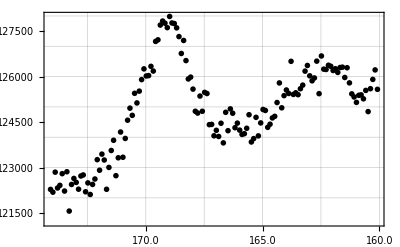

```mathematica
ListPlot[{op},ScalingFunctions->{"Reverse","Linear"}]
```

Okay, so I should now be able to make the above into a function where I provide a list of OP of files and sheet names as input and receive as output a list of ordered pairs.

```mathematica
ExtractXPSData[fn_String(*fileName *),sn_String(* Sheet name *)]:=Module[
{ri,jd,op,lds,dc},
(* Need to specify that we want the "Data" from the excel sheet, rather than the sheetnames or some other metadata.*)
ri=Import[fn,{"Data",sn}];(* ri = (R)aw (I)mport *)
lds=17;(* The (l)ine the (d)ata (s)tarts on *)
jd =ri[[lds;;]];(* jd = (J)ust (D)ata *)
dc={1,3};(* (d)ata (c)olumns  *)
op=jd[[All,dc]] (* op= (O)rdered (P)airs *)
]
SetAttributes[ExtractXPSData,Listable]
```

```mathematica
FileNames[]
```

{Au120sAged.xls,Au240s.xls,Au60s.xls,AuPreVacuum.xls,C0s.xls,C240s.xls,C60s.xls,formvar60s.xls}

```mathematica
fn={"AuPreVacuum.xls","Au60s.xls","Au120sAged.xls","Au240s.xls"};
op=ExtractXPSData[fn,sn];
ListPlot[op,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"}]
```

-Graphics-

Okay, now I need to do some re-scaling so that we can more clearly see how the datasets compare. Let’s first try just subtracting the intensity value of the right-most datapoint from each set.

```mathematica
NormalizeRightSubtract[data_]:=Apply[{#1,#2-data[[-1,2]]}&,data,{1}];
ClearAttributes[NormalizeRightSubtract,Listable]
```

```mathematica
norm1=Map[NormalizeRightSubtract,op];
```

```mathematica
ListPlot[norm1,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"}]
```

-Graphics-

It doesn’t look super great. What if we instead subtract the left-most intensity?

```mathematica
NormalizeLeftSubtract[data_]:=Apply[{#1,#2-data[[1,2]]}&,data,{1}];
norm2=Map[NormalizeLeftSubtract,op];
ListPlot[norm2,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"}]
```

-Graphics-

Not much better. Let’s take a moving average.

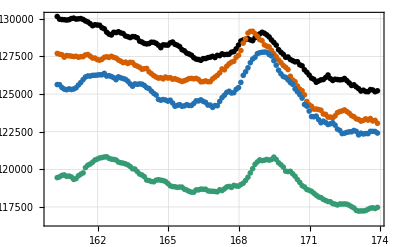

```mathematica
ma=Map[MovingAverage[#,5]&,op];
ListPlot[ma]
```

It’s not obviously better. As a final try, let’s remove a slope from the data.

```mathematica
Clear[NormalizeSlopeSubtract]
NormalizeSlopeSubtract[data_]:=Module[
{rise,run,slope,temp},
{run,rise}=data[[-1]]-data[[1]];
slope=Echo[rise/run];
temp=Apply[{#1,(#2-slope*#1)/data[[-1,2]]}&,data,{1}];
Apply[{#1,#2-temp[[-1,2]]}&,temp,{1}]
];
ClearAttributes[NormalizeSlopeSubtract,Listable]
```

```mathematica
norm3=Map[NormalizeSlopeSubtract,op];
ListPlot[norm3,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"},Joined->True]
```

-340.

-331.

-235.857

-125.143

-Graphics-

As another alternative (which I think is probably most accurate) let’s normalize to the peak.

```mathematica
Clear[NormalizeToPeak]
NormalizeToPeak[data_]:=Module[
{peak},
peak=Max[Transpose[data][[2]]];
Apply[{#1,#2/Max[peak]}&,data,{1}]
];
ClearAttributes[NormalizeToPeak,Listable]
```

```mathematica
norm3=Map[NormalizeSlopeSubtract,op];
norm4=Map[NormalizeToPeak,norm3];
ListPlot[norm4,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"},Joined->True]
```

-340.

-331.

-235.857

-125.143

0.

0.

0.

«1 more identical outputs»

-Graphics-

```mathematica
OffsetDataVertically[data_,offset_]:=Apply[{#1,#2+offset}&,data,{1}];
```

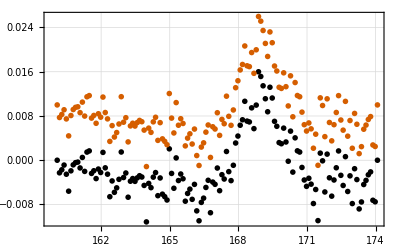

```mathematica
ListPlot[{norm3[[1]],OffsetDataVertically[norm3[[1]],.01]}]
```

None of these is really as convincing as looking at each of the plots individually on their own scale.

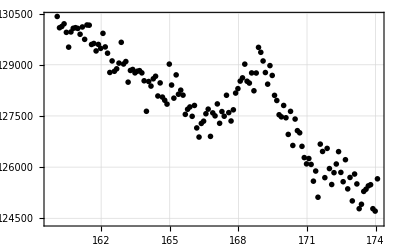
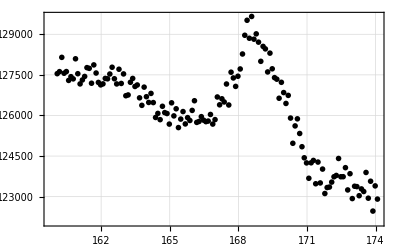
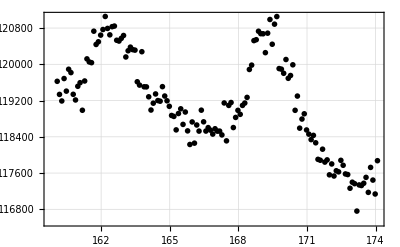
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListPlot[{#}]&,op]
```

## 2021-05-27

This time when I exported the data from the XPS machine, I put everything in one spreadsheet. I need to figure out how I can import the data.

```mathematica
$DATARUNS
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"2021","05","20"}]]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\2021\05\20

```mathematica
fn="SAM1.xls"
Import[fn]
```

SAM1.xls

{{{,,,,,,,Acquisition Parameters :,,,,,Experiment Descriptions :},{,,,,,,,,,,,,  },{,,,,,,,Parameter, ,,,,cysteineSAM2\X-Ray011 400um - FG  ON\SAM6},{,,,,,,,Total acquisition time,35.3 secs,,,,},{,,,,,,,Number of Scans,5.,,,,},148,{160.38,,132524.,,,,,,,,,,},{160.28,,130817.,,,,,,,,,,},{160.18,,131182.,,,,,,,,,,},{160.08,,132266.,,,,,,,,,,}},36,{{}}}
 |  |  |  |

```mathematica
(* Just import the sheet names? *)
sn=Import[fn,"Sheets"](* sn = Sheet Names *)
```

{S2p Scan #005 F,S2p Scan #004 F,S2p Scan #003 F,S2p Scan #002 F,S2p Scan F,Titles F,S2p Scan #005 E,S2p Scan #004 E,S2p Scan #003 E,S2p Scan #002 E,S2p Scan E,Titles E,S2p Scan #005 D,S2p Scan #004 D,S2p Scan #003 D,S2p Scan #002 D,S2p Scan D,Titles D,S2p Scan #005 C,S2p Scan #004 C,S2p Scan #003 C,S2p Scan #002 C,S2p Scan C,Titles C,S2p Scan #005 B,S2p Scan #004 B,S2p Scan #003 B,S2p Scan #002 B,S2p Scan B,Titles B,S2p Scan #002 A,S2p Scan A,S2p Scan #003 A,S2p Scan #004 A,S2p Scan #005 A,Titles A,Titles,Sheet1}

```mathematica
names=Partition[sn,6]
```

{{S2p Scan #005 F,S2p Scan #004 F,S2p Scan #003 F,S2p Scan #002 F,S2p Scan F,Titles F},{S2p Scan #005 E,S2p Scan #004 E,S2p Scan #003 E,S2p Scan #002 E,S2p Scan E,Titles E},{S2p Scan #005 D,S2p Scan #004 D,S2p Scan #003 D,S2p Scan #002 D,S2p Scan D,Titles D},{S2p Scan #005 C,S2p Scan #004 C,S2p Scan #003 C,S2p Scan #002 C,S2p Scan C,Titles C},{S2p Scan #005 B,S2p Scan #004 B,S2p Scan #003 B,S2p Scan #002 B,S2p Scan B,Titles B},{S2p Scan #002 A,S2p Scan A,S2p Scan #003 A,S2p Scan #004 A,S2p Scan #005 A,Titles A}}

Fortunately, this ExtractXPSData function is listable , making the whole thing fairly straightforward.

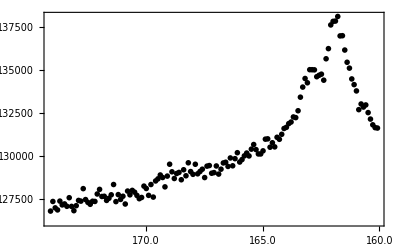

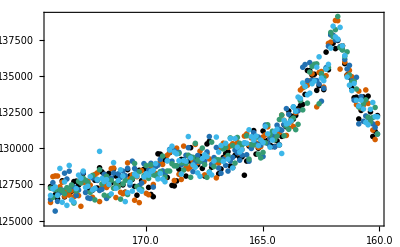

```mathematica
all=<||>;
op=ExtractXPSData[fn,names[[1]][[;;5]]];
this="SAM6"->op;
AppendTo[all,this];
ListPlot[Mean[op],ScalingFunctions->{"Reverse",Automatic}]
ListPlot[op,ScalingFunctions->{"Reverse",Automatic}]
```

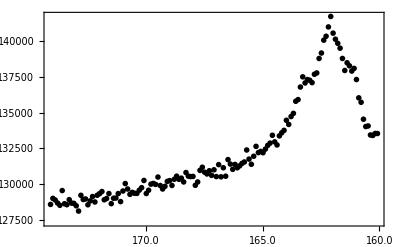

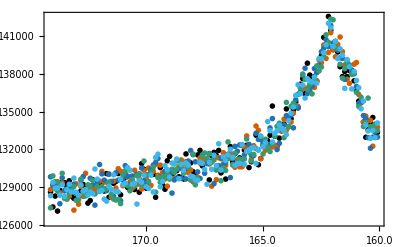

```mathematica
op=ExtractXPSData[fn,names[[2]][[;;5]]];
this="SAM5"->op;
AppendTo[all,this];
ListPlot[Mean[op],ScalingFunctions->{"Reverse",Automatic}]
ListPlot[op,ScalingFunctions->{"Reverse",Automatic}]
```

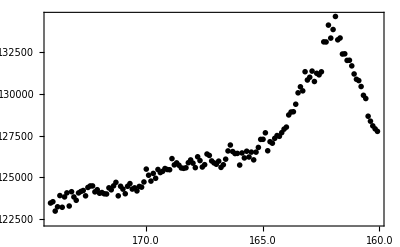

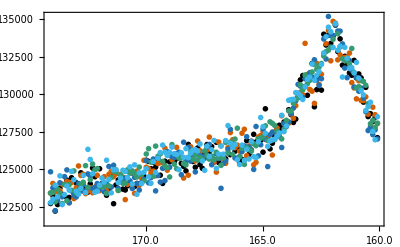

```mathematica
op=ExtractXPSData[fn,names[[3]][[;;5]]];
this="SAM4"->op;
AppendTo[all,this];
ListPlot[Mean[op],ScalingFunctions->{"Reverse",Automatic}]
ListPlot[op,ScalingFunctions->{"Reverse",Automatic}]
```

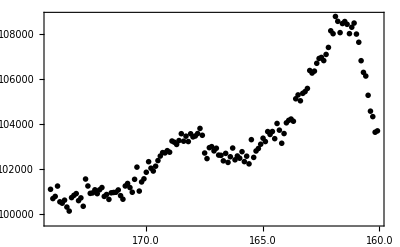

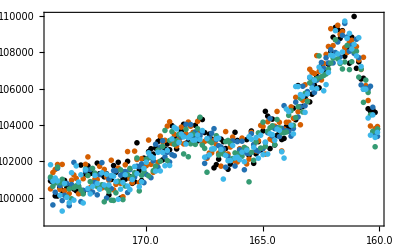

```mathematica
op=ExtractXPSData[fn,names[[4]][[;;5]]];
this="SAM3"->op;
AppendTo[all,this];
ListPlot[Mean[op],ScalingFunctions->{"Reverse",Automatic}]
ListPlot[op,ScalingFunctions->{"Reverse",Automatic}]
```

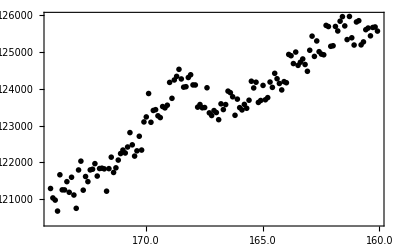

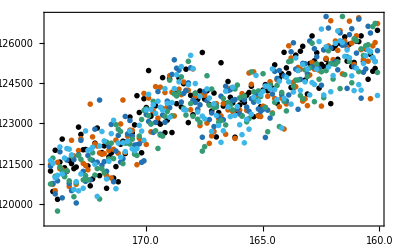

```mathematica
op=ExtractXPSData[fn,names[[5]][[;;5]]];
this="SAM2"->op;
AppendTo[all,this];
ListPlot[Mean[op],ScalingFunctions->{"Reverse",Automatic}]
ListPlot[op,ScalingFunctions->{"Reverse",Automatic}]
```

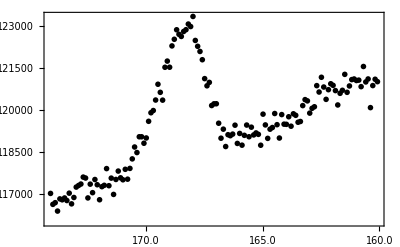

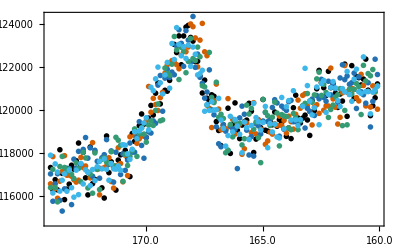

```mathematica
op=ExtractXPSData[fn,names[[6]][[;;5]]];
this="SAM1"->op;
AppendTo[all,this];
ListPlot[Mean[op],ScalingFunctions->{"Reverse",Automatic}]
ListPlot[op,ScalingFunctions->{"Reverse",Automatic}]
```

```mathematica
ListPlot[all/@Mean]
```

ListPlot::lpn: Mean is not a list of numbers or pairs of numbers.

ListPlot[Mean]

```mathematica
Thread[Mean,all]
```

Mean

```mathematica
ListPlot[{Mean[all["SAM1"]],Mean[all["SAM2"]],Mean[all["SAM3"]],Mean[all["SAM4"]],Mean[all["SAM5"]],Mean[all["SAM6"]]},PlotLabels->{"SAM1","SAM2","SAM3","SAM4","SAM5","SAM6"},FrameLabel->{"Binding Energy (eV)","Intensity (arb. units)"},PlotLabel->"Cysteine Depositied by Self-Assembly",ScalingFunctions->{"Reverse",Automatic}]
```

-Graphics-

But we should make it a bit more automated to read in multiple sheets

```mathematica
(* Just import the sheet names? *)
sn=Import[fn,"Sheets"](* sn = Sheet Names *)
```

```mathematica
scansInSet=5;
names=Partition[sn,scansInSet+1]
sets=6;
```

{{S2p Scan #005 F,S2p Scan #004 F,S2p Scan #003 F,S2p Scan #002 F,S2p Scan F,Titles F},{S2p Scan #005 E,S2p Scan #004 E,S2p Scan #003 E,S2p Scan #002 E,S2p Scan E,Titles E},{S2p Scan #005 D,S2p Scan #004 D,S2p Scan #003 D,S2p Scan #002 D,S2p Scan D,Titles D},{S2p Scan #005 C,S2p Scan #004 C,S2p Scan #003 C,S2p Scan #002 C,S2p Scan C,Titles C},{S2p Scan #005 B,S2p Scan #004 B,S2p Scan #003 B,S2p Scan #002 B,S2p Scan B,Titles B},{S2p Scan #002 A,S2p Scan A,S2p Scan #003 A,S2p Scan #004 A,S2p Scan #005 A,Titles A}}

```mathematica
all=<||>;
excelID=names[[All,6]]
op=Map[ExtractXPSData[fn,names[[#]][[;;scansInSet]]]&,Range[sets]];
Dataset[AssociationThread[excelID,op]]
```

{Titles F,Titles E,Titles D,Titles C,Titles B,Titles A}

```mathematica
res=ExtractXPSDataIdenticalSheetGroups[fn,5,6];
res[[1]]
```

{Titles F,Titles E,Titles D,Titles C,Titles B,Titles A}

```mathematica
sn=Import[fn,"Sheets"];(* sn = Sheet Names *)
names=Partition[sn,scansInSet+1]
excelID=Echo[names[[All,scansInSet+1]]]
op=AssociationMap[ExtractXPSData[fn,#[[;;scansInSet]]]&,names]
Dataset[AssociationThread[excelID,op]]
```

{{S2p Scan #005 F,S2p Scan #004 F,S2p Scan #003 F,S2p Scan #002 F,S2p Scan F,Titles F},{S2p Scan #005 E,S2p Scan #004 E,S2p Scan #003 E,S2p Scan #002 E,S2p Scan E,Titles E},{S2p Scan #005 D,S2p Scan #004 D,S2p Scan #003 D,S2p Scan #002 D,S2p Scan D,Titles D},{S2p Scan #005 C,S2p Scan #004 C,S2p Scan #003 C,S2p Scan #002 C,S2p Scan C,Titles C},{S2p Scan #005 B,S2p Scan #004 B,S2p Scan #003 B,S2p Scan #002 B,S2p Scan B,Titles B},{S2p Scan #002 A,S2p Scan A,S2p Scan #003 A,S2p Scan #004 A,S2p Scan #005 A,Titles A}}

{Titles F,Titles E,Titles D,Titles C,Titles B,Titles A}

{Titles F,Titles E,Titles D,Titles C,Titles B,Titles A}

<|{S2p Scan #005 F,S2p Scan #004 F,S2p Scan #003 F,S2p Scan #002 F,S2p Scan F,Titles F}→{<|S2p Scan #005 F→{{174.08,127356.},{173.98,127383.},{173.88,126787.},{173.78,126505.},{173.68,126968.},{173.58,127753.},{173.48,126640.},{173.38,127148.},{173.28,126832.},{173.18,127033.},{173.08,127699.},119,{161.08,133499.},{160.98,133537.},{160.88,132029.},{160.78,132620.},{160.68,133551.},{160.58,133413.},{160.48,133606.},{160.38,132524.},{160.28,130817.},{160.18,131182.},{160.08,132266.}}|>,4},4,{1}→1|>
 |  |  |  |

Dataset[<>]

Failure... Wasting too much time. Need to figure out how to have the output be an association, rather than a list of single associations.

## 2021-06-07

```mathematica
(* The plan is to write code to get the height of a peak above background *)
```

```mathematica
SetDirectory[$PACKAGES]
<<xpsProcessing`
ResetDirectory[]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\packages

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\packages

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"2021","05","20"}]]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\2021\05\20

```mathematica
fn="SAM1.xls"
Import[fn]
```

SAM1.xls

{{{,,,,,,,Acquisition Parameters :,,,,,Experiment Descriptions :},{,,,,,,,,,,,,  },{,,,,,,,Parameter, ,,,,cysteineSAM2\X-Ray011 400um - FG  ON\SAM6},{,,,,,,,Total acquisition time,35.3 secs,,,,},{,,,,,,,Number of Scans,5.,,,,},148,{160.38,,132524.,,,,,,,,,,},{160.28,,130817.,,,,,,,,,,},{160.18,,131182.,,,,,,,,,,},{160.08,,132266.,,,,,,,,,,}},36,{{}}}
 |  |  |  |

```mathematica
(* Just import the sheet names? *)
sn=Import[fn,"Sheets"](* sn = Sheet Names *)
```

{S2p Scan #005 F,S2p Scan #004 F,S2p Scan #003 F,S2p Scan #002 F,S2p Scan F,Titles F,S2p Scan #005 E,S2p Scan #004 E,S2p Scan #003 E,S2p Scan #002 E,S2p Scan E,Titles E,S2p Scan #005 D,S2p Scan #004 D,S2p Scan #003 D,S2p Scan #002 D,S2p Scan D,Titles D,S2p Scan #005 C,S2p Scan #004 C,S2p Scan #003 C,S2p Scan #002 C,S2p Scan C,Titles C,S2p Scan #005 B,S2p Scan #004 B,S2p Scan #003 B,S2p Scan #002 B,S2p Scan B,Titles B,S2p Scan #002 A,S2p Scan A,S2p Scan #003 A,S2p Scan #004 A,S2p Scan #005 A,Titles A,Titles,Sheet1}

```mathematica
names=Partition[sn,6]
```

{{S2p Scan #005 F,S2p Scan #004 F,S2p Scan #003 F,S2p Scan #002 F,S2p Scan F,Titles F},{S2p Scan #005 E,S2p Scan #004 E,S2p Scan #003 E,S2p Scan #002 E,S2p Scan E,Titles E},{S2p Scan #005 D,S2p Scan #004 D,S2p Scan #003 D,S2p Scan #002 D,S2p Scan D,Titles D},{S2p Scan #005 C,S2p Scan #004 C,S2p Scan #003 C,S2p Scan #002 C,S2p Scan C,Titles C},{S2p Scan #005 B,S2p Scan #004 B,S2p Scan #003 B,S2p Scan #002 B,S2p Scan B,Titles B},{S2p Scan #002 A,S2p Scan A,S2p Scan #003 A,S2p Scan #004 A,S2p Scan #005 A,Titles A}}

```mathematica
res=ExtractXPSDataIdenticalSheetGroups[fn,5,6];
```

```mathematica
(* I'm kind of deciding that it's easier to just do it by hand. *)
```

## 2021-06-10

```mathematica
SetDirectory[$PACKAGES]
<<xpsProcessing`
ResetDirectory[]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\packages

C:\Users\kahrendsen2\Documents

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"XPS","XPSEXPORT","2021-06-05"}]]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\XPS\XPSEXPORT\2021-06-05

```mathematica
FileNames[]
```

```mathematica
SetDirectory[FileNameJoin[{"goldControl"}]]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\XPS\XPSEXPORT\2021-06-05\goldControl

```mathematica
fn=FileNames[]
```

{x_0.xls,x_5000.xls}

```mathematica
sn=Import[fn[[1]],"Sheets"]
```

{Cu2p Scan,O1s Scan,N1s Scan,C1s Scan,S2p Scan,Au4f Scan,Peak Table,Experiment,Titles,Sheet1}

```mathematica
ExtractXPSData[fn[[2]],"S2p Scan"]
```

ExtractXPSData[x_5000.xls,S2p Scan]

The old function that I wrote didn’t account for there being multiple data lines, so it only gets the first “Y” column”

```mathematica
Clear[ExtractXPSDataMultiLine]
ExtractXPSDataMultiLine[fn_String(*fileName *), sn_String(* Sheet name *),lines_] :=
    Module[{ri, jd, op, lds, dc,dcNum},
        (* Need to specify that we want the "Data" from the excel sheet, rather than the sheetnames or some other metadata.*)
        ri = Import[fn, {"Data", sn}];(* ri = (R)aw (I)mport *)
        lds = 20;(* The (l)ine the (d)ata (s)tarts on *)
        jd = ri[[lds ;; ]];(* jd = (J)ust (D)ata *)
dcNum=Range[3,3+lines-1];
        dc = {1, 3, 4};(* (d)ata (c)olumns  *)
        op = jd[[All, {1,#}]]&/@ dcNum;(* op= (O)rdered (P)airs *)
       (* <|sn->op|>*)
       op
    ]
```

```mathematica
xpsml=ExtractXPSDataMultiLine[fn[[1]],#,2]&/@ sn[[;;-5]] (* XPS (M)ulti (L)ine *)
```

{1}
 |  |  |  |

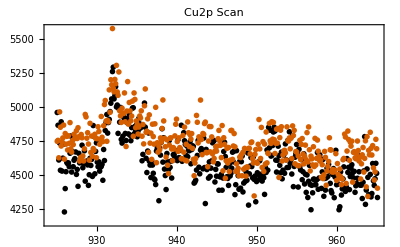
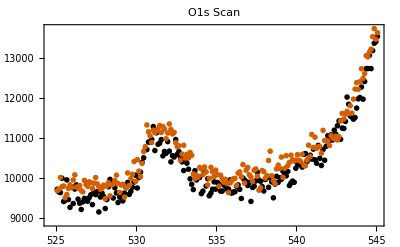
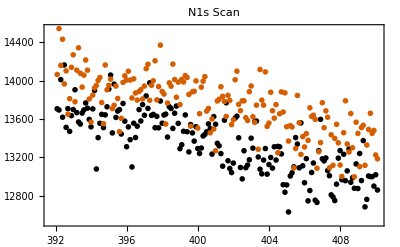
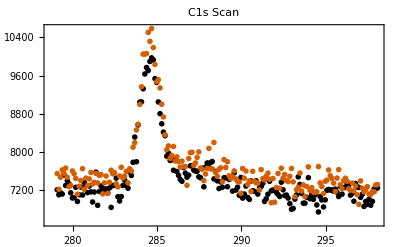
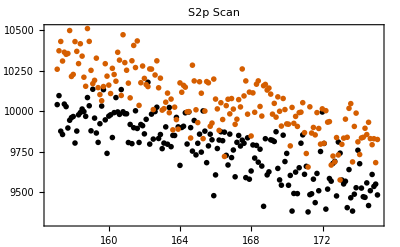
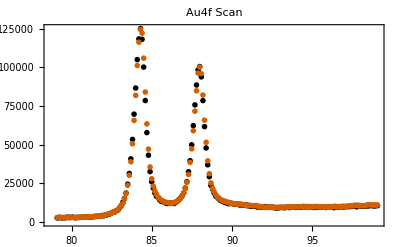

```mathematica
Apply[ListPlot[#2,PlotRange->Full,PlotLabel->#1]&,Transpose[{sn[[;;-5]],xpsml}],{1}]
```

```mathematica
xpsml2=ExtractXPSDataMultiLine[fn[[2]],#,2]&/@ sn[[;;-5]] (* XPS (M)ulti (L)ine *)
```

{{{{965.08,2545.26},{964.98,2609.51},{964.88,2669.67},{964.78,2534.66},{964.68,2592.56},{964.58,2603.01},{964.48,2674.69},{964.38,2864.72},{964.28,2738.88},{964.18,2666.95},{964.08,2747.72},{963.98,2663.26},{963.88,2523.64},{963.78,2512.73},{963.68,2483.07},{963.58,2736.48},{963.48,2691.66},{963.38,2724.1},{963.28,2607.73},363,{926.88,2853.78},{926.78,2945.3},{926.68,2881.18},{926.58,2958.31},{926.48,2835.77},{926.38,2682.86},{926.28,2756.69},{926.18,3109.56},{926.08,2890.84},{925.98,2768.4},{925.88,2865.02},{925.78,2957.45},{925.68,2745.68},{925.58,2927.98},{925.48,2830.62},{925.38,2797.29},{925.28,2949.37},{925.18,2990.23},{925.08,2925.56}},{1}},4,{1}}
 |  |  |  |

```mathematica
xpsAll=Map[Catenate,Transpose[{xpsml,xpsml2}]]
```

{1}
 |  |  |  |

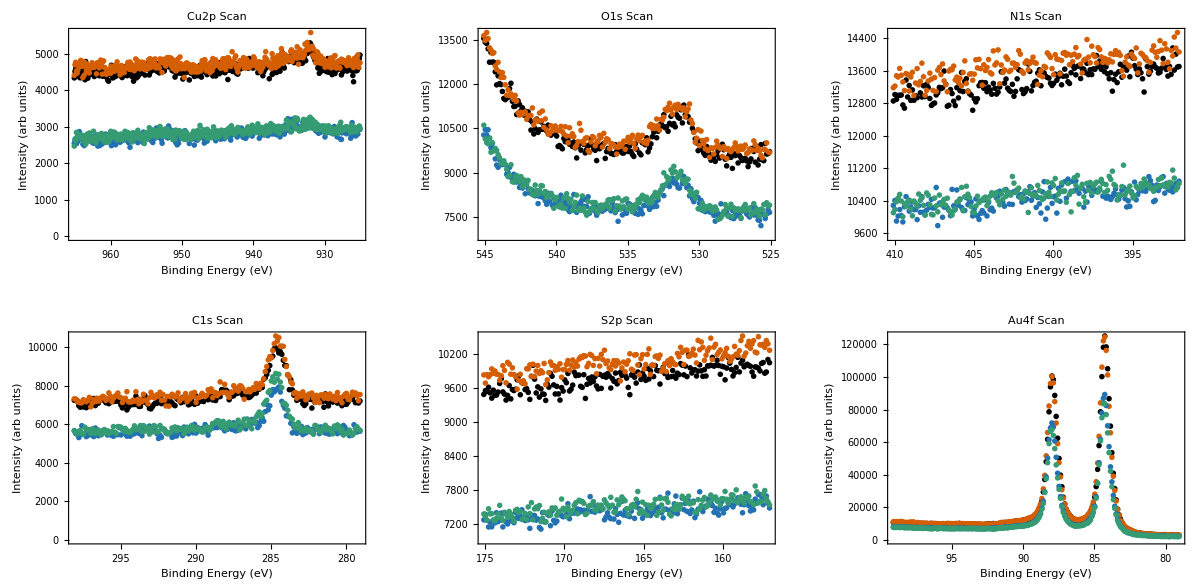

```mathematica
GraphicsGrid[Partition[Apply[ListPlot[#2,PlotRange->Full,PlotLabel->#1,ScalingFunctions->{"Reverse",Automatic},FrameLabel->{"Binding Energy (eV)","Intensity (arb units)"}]&,Transpose[{sn[[;;-5]],xpsAll}],{1}],3],ImageSize->Full]
```

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"XPS","XPSEXPORT","2021-06-05"}]]
FileNames[]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\XPS\XPSEXPORT\2021-06-05

{copperExposed,goldControl,goldExposed,goldSAM1}

```mathematica
SetDirectory[FileNameJoin[{"goldExposed"}]]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\XPS\XPSEXPORT\2021-06-05\goldExposed

```mathematica
xpsml=ExtractXPSDataMultiLine[fn[[1]],#,2]&/@ sn[[;;-5]] (* XPS (M)ulti (L)ine *)
```

{{{{965.08,38953.5},{964.98,39439.7},{964.88,39470.7},{964.78,39561.2},{964.68,39347.3},{964.58,39423.1},{964.48,39471.3},{964.38,39668.3},{964.28,39933.9},{964.18,39473.7},{964.08,40075.9},{963.98,39585.7},{963.88,39897.8},{963.78,39488.8},{963.68,40000.1},{963.58,39972.},{963.48,40134.2},{963.38,39807.8},{963.28,39561.3},363,{926.88,32666.7},{926.78,32841.5},{926.68,32494.8},{926.58,32424.1},{926.48,32677.2},{926.38,32616.2},{926.28,32479.1},{926.18,32439.1},{926.08,32888.8},{925.98,32728.4},{925.88,32485.1},{925.78,32453.5},{925.68,32625.7},{925.58,32734.3},{925.48,32178.5},{925.38,32689.9},{925.28,32153.6},{925.18,32779.5},{925.08,32728.1}},{1}},4,{1}}
 |  |  |  |

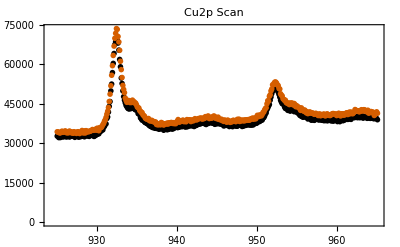
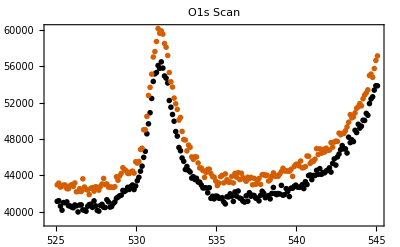
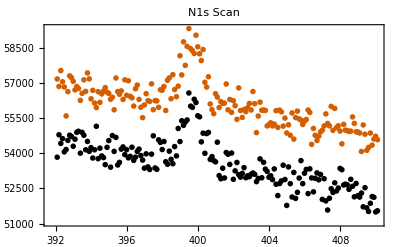
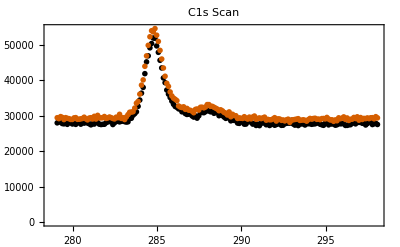
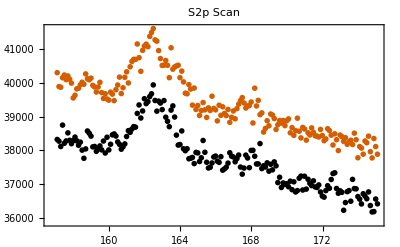
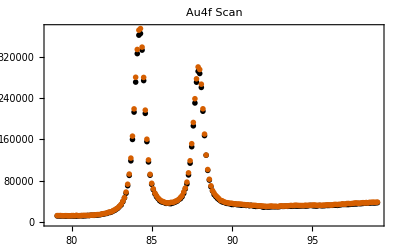

```mathematica
Apply[ListPlot[#2,PlotRange->Full,PlotLabel->#1]&,Transpose[{sn[[;;-5]],xpsml}],{1}]
```

```mathematica
xpsml2=ExtractXPSDataMultiLine[fn[[2]],#,2]&/@ sn[[;;-5]] (* XPS (M)ulti (L)ine *)
```

{{{{965.08,25651.3},{964.98,26038.},{964.88,25791.8},{964.78,25917.4},{964.68,25730.2},{964.58,26123.1},{964.48,26031.8},{964.38,25580.1},{964.28,25968.3},{964.18,26190.3},{964.08,25610.},{963.98,25810.1},{963.88,26033.6},{963.78,25709.},{963.68,25524.2},{963.58,25993.4},{963.48,25831.6},{963.38,25924.1},{963.28,25512.7},363,{926.88,21505.4},{926.78,21616.},{926.68,21269.1},{926.58,21896.2},{926.48,21479.6},{926.38,21402.6},{926.28,21512.6},{926.18,21117.2},{926.08,21383.1},{925.98,21603.5},{925.88,21665.8},{925.78,21282.6},{925.68,21400.1},{925.58,21410.2},{925.48,21421.4},{925.38,21581.3},{925.28,21201.6},{925.18,21790.4},{925.08,21545.9}},{1}},4,1}
 |  |  |  |

```mathematica
xpsAll=Map[Catenate,Transpose[{xpsml,xpsml2}]]
```

{1}
 |  |  |  |

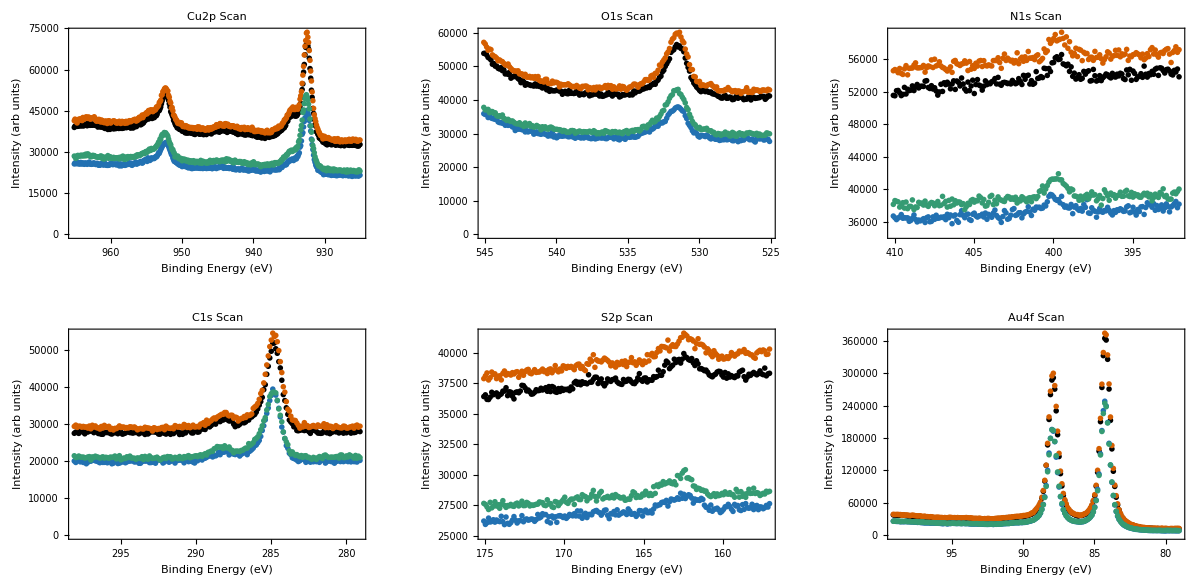

```mathematica
GraphicsGrid[Partition[Apply[ListPlot[#2,PlotRange->Full,PlotLabel->#1,ScalingFunctions->{"Reverse",Automatic},FrameLabel->{"Binding Energy (eV)","Intensity (arb units)"}]&,Transpose[{sn[[;;-5]],xpsAll}],{1}],3],ImageSize->Full]
```

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"XPS","XPSEXPORT","2021-06-05"}]]
FileNames[]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\XPS\XPSEXPORT\2021-06-05

{copperExposed,goldControl,goldExposed,goldSAM1}

SetDirectory::cdir: Cannot set current directory to copperExposed.

$Failed

{{{{965.08,10552.7},{964.98,10436.8},{964.88,10676.3},{964.78,10631.3},{964.68,10482.1},{964.58,10737.3},{964.48,10515.3},{964.38,10811.7},{964.28,10753.3},{964.18,10499.5},{964.08,10682.2},{963.98,10839.4},{963.88,10765.7},{963.78,10727.1},{963.68,10559.9},{963.58,10872.4},{963.48,10549.5},{963.38,10505.3},{963.28,10585.5},363,{926.88,9737.45},{926.78,9797.09},{926.68,9816.58},{926.58,9674.78},{926.48,9803.12},{926.38,9795.58},{926.28,9440.37},{926.18,9888.99},{926.08,9928.06},{925.98,9722.28},{925.88,10041.},{925.78,9892.39},{925.68,9889.39},{925.58,9852.},{925.48,9793.38},{925.38,9644.81},{925.28,9877.43},{925.18,9810.15},{925.08,9868.13}},{1}},4,{1}}
 |  |  |  |

{{{{965.08,18133.3},{964.98,18213.6},{964.88,18037.9},{964.78,18343.2},{964.68,18026.1},{964.58,17840.4},{964.48,17783.7},{964.38,17744.},{964.28,17837.8},{964.18,17756.9},{964.08,17925.8},{963.98,17924.5},{963.88,18028.8},{963.78,17961.3},{963.68,18386.1},{963.58,18032.3},{963.48,18147.},{963.38,17991.4},{963.28,18038.4},363,{926.88,15376.5},{926.78,15603.3},{926.68,15341.},{926.58,15380.6},{926.48,15407.1},{926.38,15294.5},{926.28,15647.7},{926.18,15317.7},{926.08,15303.5},{925.98,15049.8},{925.88,15333.7},{925.78,15507.2},{925.68,15391.7},{925.58,15514.8},{925.48,15279.5},{925.38,15668.6},{925.28,15499.4},{925.18,15241.3},{925.08,15706.8}},{1}},4,{1}}
 |  |  |  |

{1,4,{{{99.08,1551.4},{98.98,1412.13},{98.88,1430.53},{98.78,1418.15},{98.68,1465.3},{98.58,1503.88},{98.48,1408.73},{98.38,1383.01},{98.28,1322.16},{98.18,1436.39},{98.08,1413.49},{97.98,1399.83},{97.88,1499.84},{97.78,1450.62},{97.68,1330.11},{97.58,1482.71},{97.48,1418.13},{97.38,1365.91},{97.28,1456.36},{97.18,1338.96},161,{80.98,1104.6},{80.88,1076.38},{80.78,1119.37},{80.68,1045.26},{80.58,1080.71},{80.48,1168.68},{80.38,1153.38},{80.28,1244.16},{80.18,1203.8},{80.08,1066.98},{79.98,1143.6},{79.88,1251.21},{79.78,1259.51},{79.68,1138.15},{79.58,1311.51},{79.48,1280.87},{79.38,1298.59},{79.28,1208.81},{79.18,1285.05},{79.08,1296.1}},2,{1}}}
 |  |  |  |

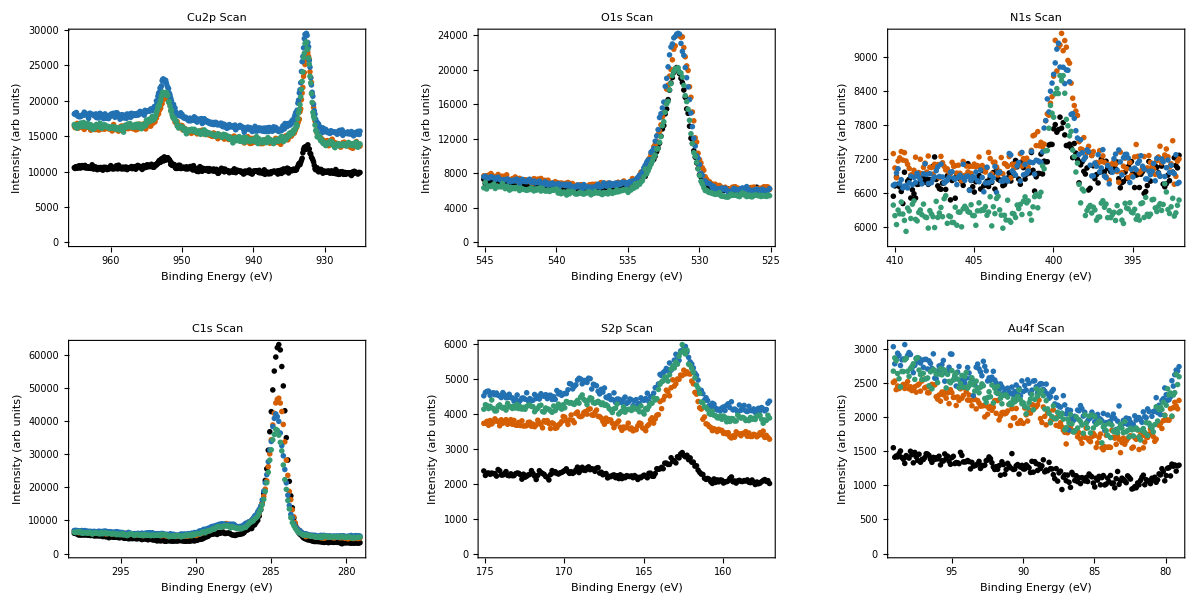

```mathematica
SetDirectory[FileNameJoin[{"copperExposed"}]]
xpsml=ExtractXPSDataMultiLine[fn[[1]],#,2]&/@ sn[[;;-5]] (* XPS (M)ulti (L)ine *)
Apply[ListPlot[#2,PlotRange->Full,PlotLabel->#1]&,Transpose[{sn[[;;-5]],xpsml}],{1}];
xpsml2=ExtractXPSDataMultiLine[fn[[2]],#,2]&/@ sn[[;;-5]] (* XPS (M)ulti (L)ine *)
xpsAll=Map[Catenate,Transpose[{xpsml,xpsml2}]]
GraphicsGrid[Partition[Apply[ListPlot[#2,PlotRange->Full,PlotLabel->#1,ScalingFunctions->{"Reverse",Automatic},FrameLabel->{"Binding Energy (eV)","Intensity (arb units)"}]&,Transpose[{sn[[;;-5]],xpsAll}],{1}],3],ImageSize->Full]
```